### Defining Constants:

```mathematica
G=6.6743 10^-11;
Λminus=((8 Pi G ρcritpl)/c^2)/1.001;
c=299792.458 10^3;
H0pl=3.23hplanck 10^(−18);
hplanck=0.6770;
ρcritpl=(3 H0pl^2)/(8 Pi G);
λ=1;
Λplus=(8 Pi G ρcritpl)/c^2;
Rst=((3 G (mminus))/(Λ c^2))^(1/3);
mminus=  10^10(1.988416 10^30);
mplus=1.001 10^10(1.988416 10^30);
w0=-0.5;
```

```mathematica
rs=Solve[r^3+(6 G mminus)/(c^2 Λminus)-(3 r)/Λminus==0,r,Reals]
```

{{r→-1.37166×10^26},{r→2.95326×10^13},{r→1.37166×10^26}}

```mathematica
rch=Solve[r^3+(6 G mplus)/(c^2 Λplus)-(3 r)/Λplus==0,r,Reals]
```

{{r→-1.37097×10^26},{r→2.95621×10^13},{r→1.37097×10^26}}

```mathematica
rsds=Solve[r^3+(6 G mminus)/(c^2 Λplus)-(3 r)/Λplus==0,r,Reals]
```

{{r→-1.37097×10^26},{r→2.95326×10^13},{r→1.37097×10^26}}

### m=(m_++m_-)/2, μ+=m_+/m, μ-=m_-/m, Λ=(Λ_++Λ_-)/2, λ+=Λ_+/Λ, λ-=Λ_-/Λ, xs= (2G m/c^2) Λ^(1/2), r=(Λ^(1/2) R)

```mathematica
m=(mminus+mplus)/2;
Λ=(Λminus+Λplus)/2;

q=mplus/mminus;
qp=Λplus/ Λminus;

xs=(2 G m)/c^2 Λ^(1/2);
μminus=mminus/m;
λminus=Λminus/Λ;
```

### Finding solutions for σ0 nand R0 for static stable shells:

```mathematica
(*Veff''(R0)*)
Veffpp=(-18 (1+q) x0^3 xs μminus+(-6 (-1+q) (-1+qp) x0^3 xs (3+2 w0 (7+6 w0-2 λ)-4 λ) λminus μminus-18 (-1+q)^2 xs^2 (w0 (1+6 w0)-2 (1+w0) λ) μminus^2+x0^6 (-(-1+qp)^2 (15+26 w0+12 w0^2-4 (1+w0) λ) λminus^2-6 (1+qp) λminus σ0^2-9 (3+6 w0+4 w0^2+4 (1+w0) λ) σ0^4))/σ0^2)/(36 x0^6);

(*Solving the Algebraic system of Equations (38) and (39) here, by imposing Veff''(Subscript[R, 0])>0 and condition (41)*)
eq38=-(((-1+qp) x0^3 λminus+3 (-1+q) xs μminus)^2+6 x0^3 (-6 x0+(1+qp) x0^3 λminus+3 (1+q) xs μminus) σ0^2+9 x0^6 σ0^4)/(72 x0^4 σ0^2)==0;
eq39=-(18 (-1+q)^2 w0 xs^2 μminus^2+3 x0^3 xs μminus ((-1+q) (-1+qp) (3+4 w0) λminus-3 (1+q) σ0^2)+x0^6 ((-1+qp)^2 (3+2 w0) λminus^2+6 (1+qp) λminus σ0^2-9 (1+2 w0) σ0^4))/(36 x0^5 σ0^2)==0;
sigma0cond=-(xs μminus)/x0(q-1)-x0^2/3 λminus(qp-1);
R0σ0=FindInstance[{eq78,eq79,sigma0cond<0,Veffpp>0,x0>0,σ0>0},{x0,σ0},Reals]
```

{{x0→0.0000824159,σ0→4.11873×10^-8}}

```mathematica
x01=R0σ0[[1,1,2]]
R01=x01 Λ^(-1/2) (*Subscript[R, 0] in meters*)
σ01=R0σ0[[1,2,2]]
sigma0=((4 Pi G)/(c^2 Λ^(1/2)))^-1 σ01 (*Subscript[σ, 0] in kg/m^2*)
```

0.0000824159

6.52512×10^21

4.11873×10^-8

5.57458×10^-8

```mathematica
sinthetanoshell[r_]:=((√(1-(2 G mminus)/(c^2 r)-1/3*Λplus r^2)((3 √3 G mminus)/(c^2 √(1-9 ((G mminus)^2 Λplus)/c^4))))/r)
θcrit[r_]:=ArcSin[sinthetanoshell[r]]


bcrit=(3 √3 G mminus)/(c^2 √(1-9 ((G mminus)^2 Λminus)/c^4));
sinTheta[r_]:=Piecewise[{{(√(1-(2 G mminus)/(c^2 r)-1/3*Λminus r^2)bcrit)/r,r<=R01 },{(√(1-(2 G mminus)/(c^2 R01)-1/3*Λminus R01^2)bcrit)/r(√(1-(2 G mplus)/(c^2 r)-1/3*Λplus r^2))/(√(1-(2 G mplus)/(c^2 R01)-1/3*Λplus R01^2)),r>R01 }}]
Thetacrit[r_]:=ArcSin[sinTheta[r]]


θcritFull[r_]:=Piecewise[{{Pi-θcrit[r],r<=3 G mminus/c^2 },{θcrit[r],r>3 G mminus/c^2 }}]

ThetaFull[r_]:=Piecewise[{{Pi-Thetacrit[r],r<=3 G mminus/c^2 },{Thetacrit[r],3 G mminus/c^2<r }}]
```

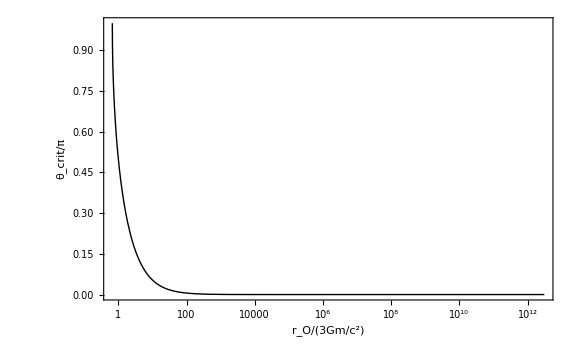

```mathematica
Plot00a=LogLinearPlot[{θcritFull[r 4.42989*10^13]/Pi},{r,rsds[[2,1,2]]/(3 G mminus/c^2),rsds[[3,1,2]]/(3 G mminus/c^2)},Frame->True,FrameLabel->{Style["r_O/(3Gm/c^2)",20,Bold],Style["θ_crit/π",20,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Black,Thick},{Blue,Thick,DotDashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18}]
```

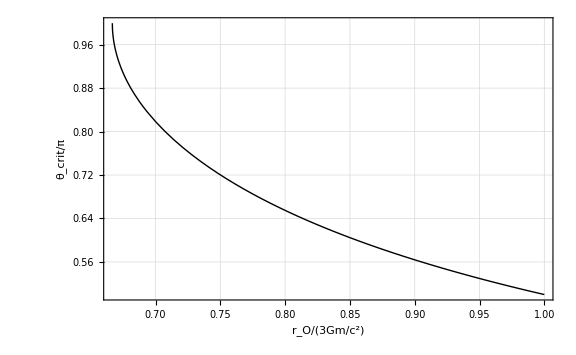

```mathematica
Plot00b=Plot[{θcritFull[r 4.42989*10^13]/Pi},{r,(2.95326*10^13)/(4.42989*10^13),1},Frame->True,FrameLabel->{Style["r_O/(3Gm/c^2)",20,Bold],Style["θ_crit/π",20,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Black,Thick},{Blue,Thick,DotDashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18}]
```

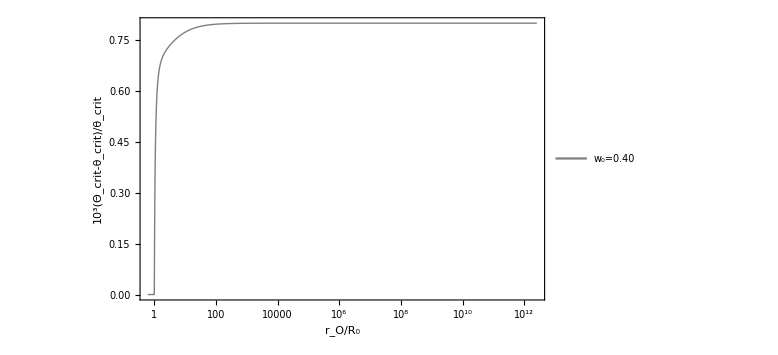

```mathematica
Plot1=LogLinearPlot[{10^3(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01]},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^3(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Gray,Thick},{Blue,Thick,DotDashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=0.40",25]},LegendMargins->5],{0.8,0.9}   (*position inside the plot*)]]
```

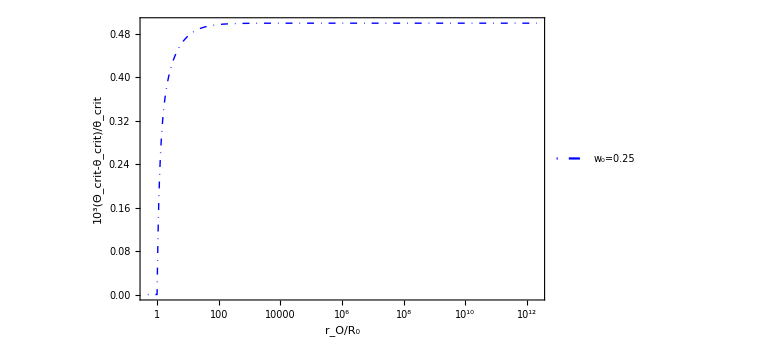

```mathematica
Plot2=LogLinearPlot[{10^3(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01]},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^3(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Blue,Thick,DotDashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=0.25",25]},LegendMargins->5],{0.8,0.8}   (*position inside the plot*)]]
```

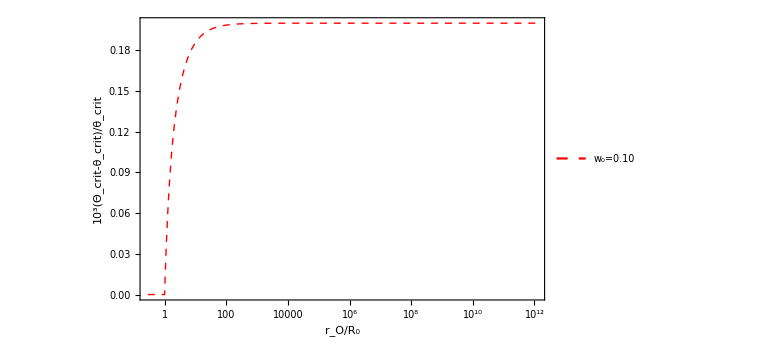

```mathematica
Plot3=LogLinearPlot[{10^3(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01]},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^3(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Red,Thick,Dashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=0.10",25]},LegendMargins->5],{0.8,0.7}   (*position inside the plot*)]]
```

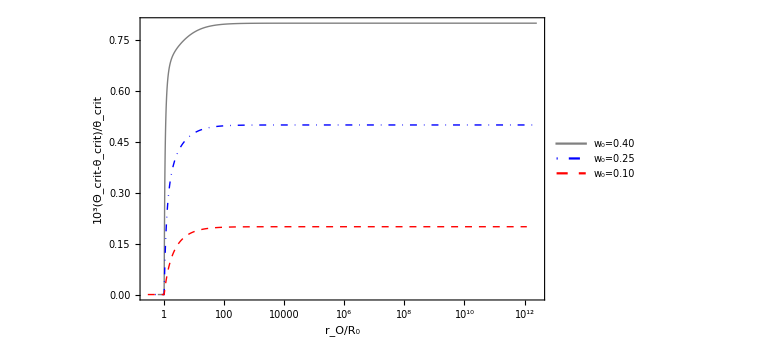

```mathematica
Show[Plot1,Plot2,Plot3]
```

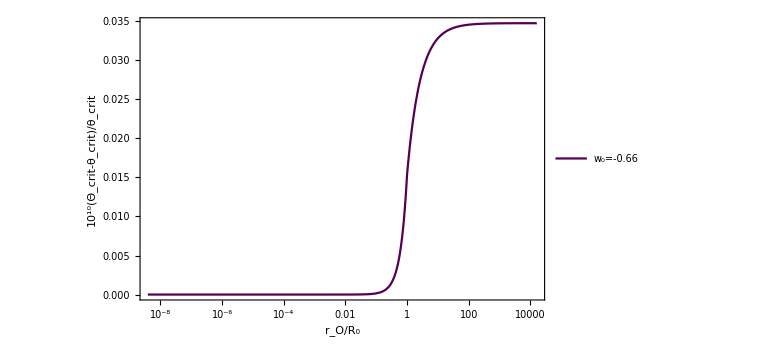

```mathematica
Plot1de=LogLinearPlot[{(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01] 10^10},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^10(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Darker[Purple]}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=-0.66",25]},LegendMargins->5],{0.2,0.7}   (*position inside the plot*)]]
```

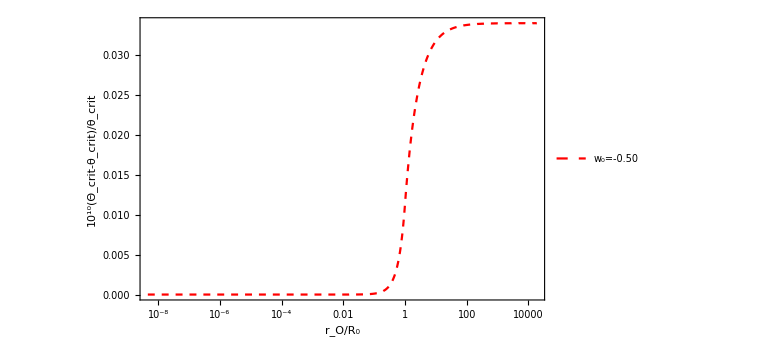

```mathematica
Plot2de=LogLinearPlot[{(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01] 10^10},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^10(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Red,Dashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=-0.50",25]},LegendMargins->5],{0.2,0.5}   (*position inside the plot*)]]
```

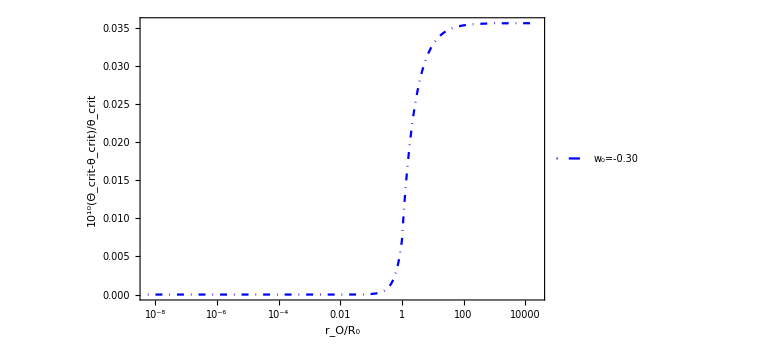

```mathematica
Plot3de=LogLinearPlot[{(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01] 10^10},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^10(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Blue,DotDashed}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=-0.30",25]},LegendMargins->5],{0.2,0.8}   (*position inside the plot*)]]
```

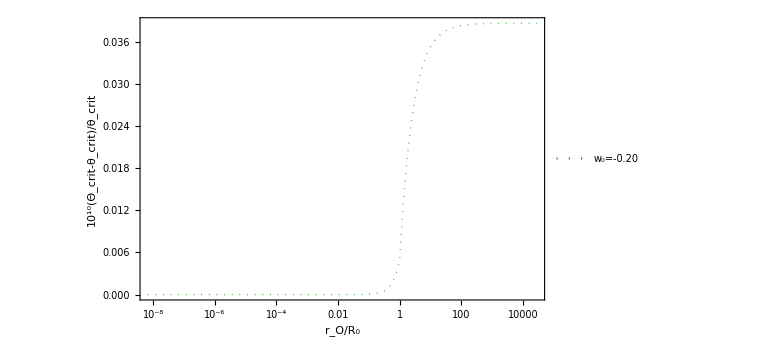

```mathematica
Plot4de=LogLinearPlot[{(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01] 10^10},{r,rs[[2,1,2]]/R01,0.9 rch[[3,1,2]]/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^10(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Darker[Green],Dotted,Thick}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=-0.20",25]},LegendMargins->5],{0.2,0.9}   (*position inside the plot*)]]
```

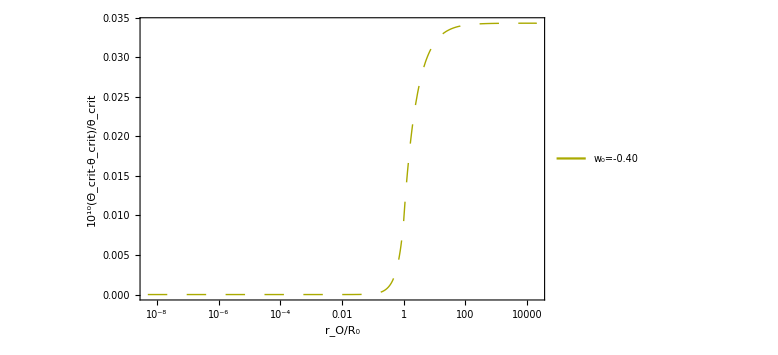

```mathematica
Plot5de=LogLinearPlot[{(-θcritFull[r R01]+ThetaFull[r R01])/θcritFull[r R01] 10^10},{r,rs[[2,1,2]]/R01,(0.9 rch[[3,1,2]])/R01},Frame->True,FrameLabel->{Style["r_O/R_0",25,Bold],Style["10^10(Θ_crit-θ_crit)/θ_crit",25,Bold]},FrameStyle->Thick,PlotRange->All,GridLines->Automatic,GridLinesStyle->LightGray,Axes->False,PlotStyle->{{Darker[Yellow],Dashing[Large],Thick}},ImageSize->Large,LabelStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{Style["w_0=-0.40",25]},LegendMargins->5],{0.2,0.6}   (*position inside the plot*)]]
```

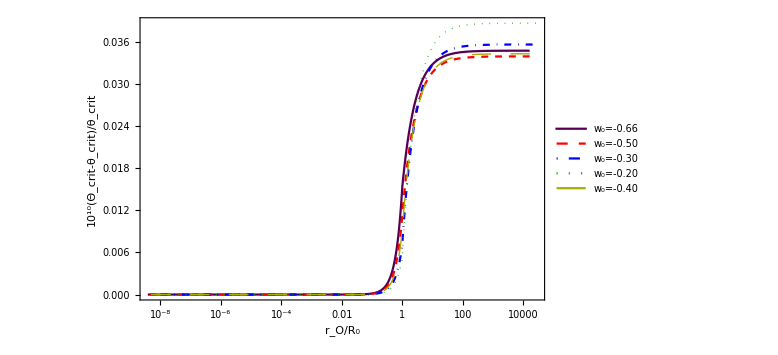

```mathematica
Show[Plot1de,Plot2de,Plot3de,Plot4de,Plot5de]
```